```mathematica
(*Funcion para importar los datos*)
importData[dir_]:=Module[{data,lambda,dataRF},
data=Import[dir];
lambda=data[[All,1]];
dataRF=Transpose[{lambda,data[[All,2]]*(10^(18))}]]
```

```mathematica
Alfinefiner=importData["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-licenciatura\\COMSOL\\Al_sph10_fine_finer.csv"];
Al20102015=importData["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-licenciatura\\COMSOL\\Al_sph_10_20_10_20_15.csv"];
Al1052015=importData["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-licenciatura\\COMSOL\\Al_sph_10_10_5_20_15.csv"];
Al1051510=importData["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-licenciatura\\COMSOL\\Al_sph_10_10_5_15_10.csv"];
Al10573=importData["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-licenciatura\\COMSOL\\Al_sph_10_10_5_7_3.csv"];
Al201073=importData["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-licenciatura\\COMSOL\\Al_sph_10_20_10_7_3.csv"];
Al2010105=importData["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-licenciatura\\COMSOL\\Al_sph_10_20_10_10_5.csv"];
```

```mathematica
(*Importar datos experimentales del aluminio*)
```

```mathematica
dataAln=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-licenciatura\\Funciones_dielectricas\\Al_Hagemann_n.csv"];
dataAlk=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-licenciatura\\Funciones_dielectricas\\Al_Hagemann_k.csv"];
lambdaAl=dataAln[[All,1]]*1000; (*λ en nm*)
nal=dataAln[[All,2]];
kAl=dataAlk[[All,2]];
nAl=nal+ I kAl;
dataAlRI=Transpose[{lambdaAl,nAl}];
alRI=Interpolation[dataAlRI]
```

```mathematica
alCextMie=Table[{λ,mieQext[alRI[λ],1,10,λ][[3]]},{λ,400,1000,10}];
lambdas=Range[400,1000,10];
```

```mathematica
(*Calcular el error*)
```

```mathematica
errorCOMSOLMie[mie_,comsol_,j_]:=Abs[mie[[All,2]][[j]]-comsol[[All,2]][[j]]]/mie[[All,2]][[j]];
```

```mathematica
errores=Table[{lambdas[[j]],errorCOMSOLMie[alCextMie,#,j]},{j,1,61}]&/@{Al201073,Al2010105};
```

```mathematica
Mean[errores[[1]][[All,2]]]
Mean[errores[[2]][[All,2]]]
```

0.0236682

0.0185565

0.0236682

```mathematica
Max[errores[[#]][[All,2]]]&/@{1,2,3,4,5,6,7}
```

{0.0755587,0.0472762,0.0472762,0.0483821,0.0566238,0.0530622,0.0539115}

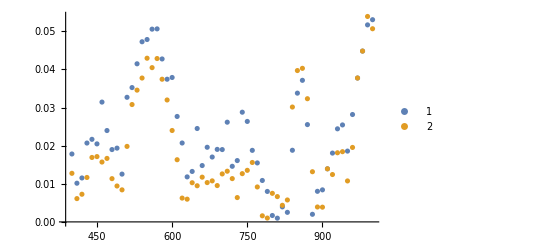

```mathematica
ListPlot[errores,PlotLegends->Automatic]
```

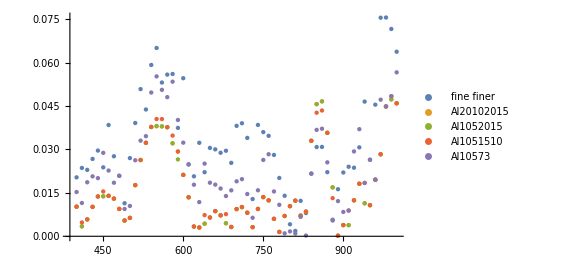

```mathematica
alCextMie8000=Table[{λ,mieQext[alRI[λ],1,8000,λ][[3]]},{λ,320000,800000,8000}];
lambdas8000=Range[400,1000,10];
```

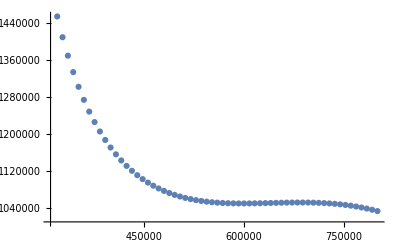

```mathematica
ListPlot[alCextMie8000]
```

```mathematica
alCextMie8000=Table[{λ,mieQext[alRI[λ],1,8000,λ][[3]]},{λ,400,1000,10}];
```

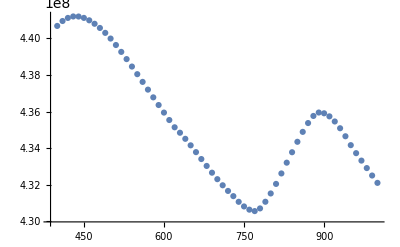

```mathematica
ListPlot[alCextMie8000]
```